```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*graphDataMany*)
```

```mathematica
data =Partition[ReadList["./graphDataMany.txt", Real], 2];
min = data[[1]][[2]];
minTau = data[[1]][[1]];
index = 1;
stationary=data;
For[i = 1, i < Length[data], ++i, 

If[data[[i]][[2]] < min, 
min = data[[i]][[2]];
minTau = data[[i]][[1]];
index = i;
];
stationary[[i]] = {data[[i]][[1]], data[[i]][[1]]*data[[i]][[2]]}
]
```

```mathematica
minPoint = {minTau, min}
```

{0.03528,27.}

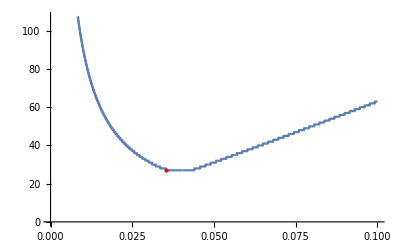

```mathematica
ListLinePlot[{data}, Epilog->{Red,PointSize@Large,Point[minPoint]}]
```

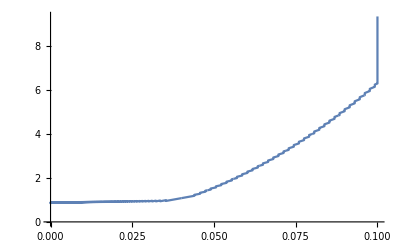

```mathematica
ListLinePlot[{stationary}]
```

```mathematica
diff =Partition[ReadList["./diffGraph.txt", Real], 3];
ListPointPlot3D[diff, AxesLabel->{"x", "y", "u"}]
```

-Graphics3D-

```mathematica
st[a_, b_, N1_, N2_]:=1/Pi(a^2/N1^2+b^2/N2^2)^(1/2)(1/a^2+1/b^2)^(-1/2);
st[1, 1, 10, 10]//N
```

0.031831